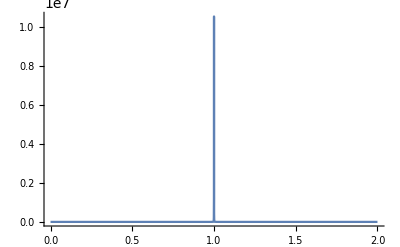

```mathematica
C0=1;C2=2;C4=1;C6=0;Plot[1/(C0-C2*q^2+C4*q^4),{q,0,2},PlotRange->All]
```

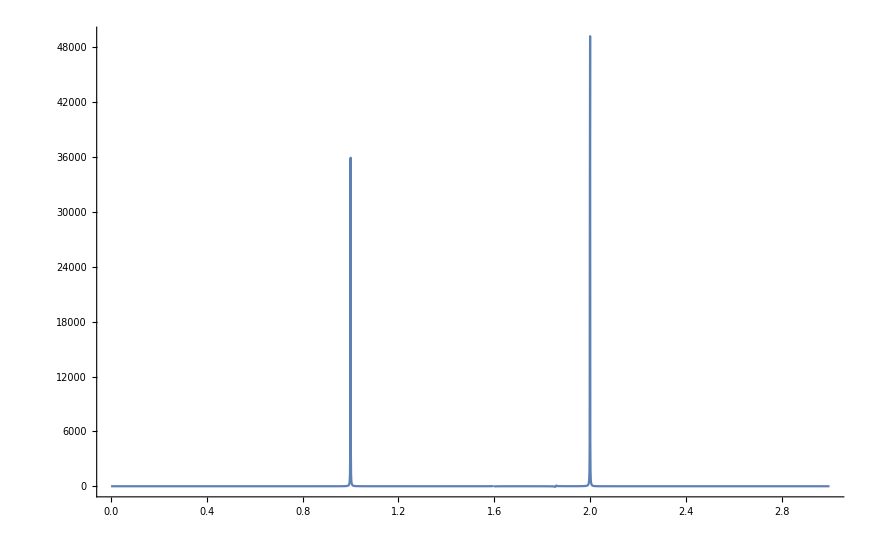

```mathematica
km1=1;km2=√3;km3=2;b1=0;b2=-0.2;b3=0.0000001;Plot[1/((km1^4-2*km1^2*k^2+k^4+b1)*(km2^4-2*km2^2*k^2+k^4+b2)*(km3^4-2*km3^2*k^2+k^4+b3)),{k,0,3},PlotRange->All]
```

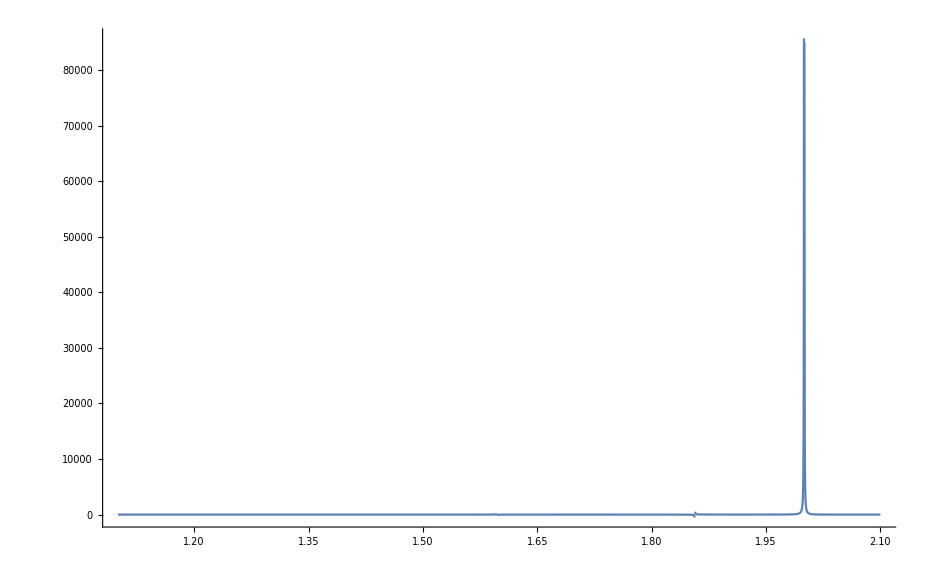

```mathematica
Plot[1/(((km1^2+(I*k)^2)^2+b1)((km2^2+(I*k)^2)^2+b2)((km3^2+(I*k)^2)^2+b3)),{k,1.1,2.1},PlotRange->All]
```

```mathematica
((km1^2+(I*k)^2)^2+b1)((km2^2+(I*k)^2)^2+b2)((km3^2+(I*k)^2)^2+b3)//Expand
```

149.04-468.88 k^2+564.04 k^4-331.6 k^6+102.4 k^8-16 k^10+k^12

```mathematica
((km1^4-2*km1^2*k^2+k^4+b1)*(km2^4-2*km2^2*k^2+k^4+b2)*(km3^4-2*km3^2*k^2+k^4+b3))//Expand
```

149.04-468.88 k^2+564.04 k^4-331.6 k^6+102.4 k^8-16 k^10+k^12